Supplementary material for
https : // arxiv.org/abs/1704.05840
coded by J Fuentes
 jfuentes[at] fis.cinvestav.mx

Beta Maps

```mathematica
ClearAll["Global`*"]
```

1: squeezing

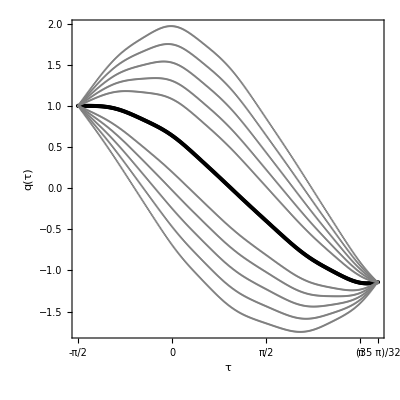

/Users/fuentes/Dropbox/qBB.jpg

```mathematica
x1 = Import["/Users/fuentes/Documents/MATLAB/x1.dat"];

an1 = Import["/Users/fuentes/Documents/MATLAB/an1.dat"];
bn1 = Import["/Users/fuentes/Documents/MATLAB/bn1.dat"];
cn1 = Import["/Users/fuentes/Documents/MATLAB/cn1.dat"];
dn1 = Import["/Users/fuentes/Documents/MATLAB/dn1.dat"];
en1 = Import["/Users/fuentes/Documents/MATLAB/en1.dat"];


ap1 = Import["/Users/fuentes/Documents/MATLAB/ap1.dat"];
bp1 = Import["/Users/fuentes/Documents/MATLAB/bp1.dat"];
cp1 = Import["/Users/fuentes/Documents/MATLAB/cp1.dat"];
dp1 = Import["/Users/fuentes/Documents/MATLAB/dp1.dat"];
ep1 = Import["/Users/fuentes/Documents/MATLAB/ep1.dat"];

x0 =x1[[All,1]];

an = an1[[All,1]];
bn = bn1[[All,1]];
cn =cn1[[All,1]];
dn = dn1[[All,1]];
en = en1[[All,1]];

ap = ap1[[All,1]];
bp =bp1[[All,1]];
cp = cp1[[All,1]];
dp = dp1[[All,1]];
ep = ep1[[All,1]];

t0 = Array[#&,Length[x0],{-π/2,35π/32}];

q0=ListPlot[
Thread[{t0,x0}],
PlotStyle->Black
];

qx=ListPlot[
{
Thread[{t0,an}],
Thread[{t0,bn}],
Thread[{t0,cn}],
Thread[{t0,dn}],
Thread[{t0,en}],
Thread[{t0,ap}],
Thread[{t0,bp}],
Thread[{t0,cp}],
Thread[{t0,dp}],
Thread[{t0,ep}]
},
PlotStyle->Gray
];

txr={-π/2,0,π/2,π,35π/32};

XTicks={
txr,
Automatic
};

maps = Show[
q0,
qx,
PlotRange->All,
AspectRatio->1,
Frame -> True,
FrameStyle->FontSize->12,
FrameLabel->{"τ","q(τ)"},
FrameTicks->XTicks
]

Export[
"/Users/fuentes/Dropbox/q_B.jpg",maps,"JPEG",
ImageResolution-> 300
]
```

```mathematica
ClearAll["Global`*"]
```

1: shadows

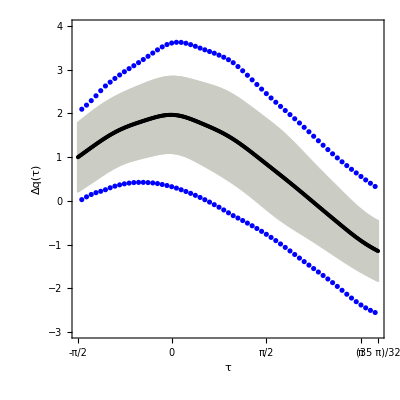

/Users/fuentes/Dropbox/s_B.jpg

```mathematica
Needs["ErrorBarPlots`"]

b1 = Import["/Users/fuentes/Documents/MATLAB/beta1.dat"];
x1 = Import["/Users/fuentes/Documents/MATLAB/trajectory1.dat"];
h0 = Import["/Users/fuentes/Documents/MATLAB/shadow.dat"];
pr = Import["/Users/fuentes/Documents/MATLAB/prob.dat"];

beta1={{-1.1412,0.007},{0.153,-0.8752}};

l0 =Abs[beta1[[1,1]]];

h0=h0[[All,1]];
hx=Reverse[h0];

z0 = Table[0,{j,1,Length[x0]}];
x0 = x1[[All,1]];
t0 = Array[#&,Length[x0],{-π/2,35π/32}];

pl =pr[[All,2]]; 
pr =pr[[All,3]]; 

txr={-π/2,0,π/2,π,35π/32};
txl ={1,100,200,300,Length[x1]};

XTicks={
Thread[{txl,txr}],
Automatic
};

dat=Partition[Riffle[x0,hx],2];

pro = ListPlot[
{pl,pr},
PlotStyle->Blue
];

bar = ErrorListPlot[
dat,
PlotStyle->ColorData[34,3],
Joined->False
];

tra=ListPlot[
x0,
PlotStyle->Black
];

maps=Show[
bar,
tra,
pro,
PlotRange->{-3,4},
PlotRange->All,
AspectRatio->1,
Frame -> True,
FrameStyle->FontSize->12,
FrameLabel->{"τ","Δq(τ)"},
FrameTicks->XTicks
]

Export[
"/Users/fuentes/Dropbox/s_B.jpg",maps,"JPEG",
ImageResolution-> 300
]
```